# Analytical calculations for M = 1

## Computing y, z, g, h for a finite population size

```mathematica
γ[n_,p_]:=1-(n*p)/(2(n-1))
ρ2[n_,p_,t2_]:=(1-2/n^2 γ[n,p])^(t2-1)(2/n^2 γ[n,p])
ρ3[n_,p_,t3_,t2_]:=((1-(2γ[n,p])/n^2)(1-(4γ[n,p])/n^2))^(t3-1)*3(1-(2γ[n,p])/n^2)^t2((2γ[n,p])/n^2)^2//FullSimplify
```

### Computing y = P(s_ia=s_ja|i ≠j) = ∑_(t=1)^∞ P(s_ia=s_ja|i ≠j,Δ_ij=t)P(Δ_ij=t) = ∑_(t=1)^∞ y(t) P(Δ_ij=t)

```mathematica
yt[n_,p_,u_,t2_]:=1/2(1+(1-u/n γ[n,p])^(2t2)) (*exact expresison, before taking the N->∞ limit*)
ycalc2[n_,p_,u_]=∑_(t2=1)^∞ yt[n,p,u,t2]*ρ2[n,p,t2]//FullSimplify
```

(8 (-1+n)^2 n^2+4 (-1+n) n (4+n (-4-n+n^2+2 p)) u+(2+n (-2+p)) (4+n (-4-n+n^2+2 p)) u^2)/(8 (-1+n)^2 n^2+8 (-1+n) n (2+n (-2+(-1+n) n+p)) u+2 (2+n (-2+p)) (2+n (-2+(-1+n) n+p)) u^2)

```mathematica
(*ycalc2[n,p,u] *)
```

### Computing z = <h_i h_j|i ≠j>= ∑_(t=1)^∞ <h_i h_j|i ≠j,Δ_ij=t>P(Δ_ij=t) = ∑_(t=1)^∞ z(t) P(Δ_ij=t)

```mathematica
zt[n_,p_,v_,t2_]:=(1-v/n γ[n,p])^(2t2) (*exact expresison, before taking the N->∞ limit*)
zcalc2[n_,p_,v_]=∑_(t2=1)^∞ zt[n,p,v,t2]*ρ2[n,p,t2]//FullSimplify
```

(2 (-1+n) n+(2+n (-2+p)) v)^2/(4 (-1+n)^2 n^2+4 (-1+n) n (2+n (-2+(-1+n) n+p)) v+(2+n (-2+p)) (2+n (-2+(-1+n) n+p)) v^2)

```mathematica
(*zcalc2[n,p,v] *)
```

### Computing g = <h_i h_j*I(s_ia=s_ja)|i ≠j>= ∑_(t=1)^∞ <h_i h_j I(s_ia=s_ja)|i ≠j,Δ_ij=t>P(Δ_ij=t) = ∑_(t=1)^∞ g(t) P(Δ_ij=t)

```mathematica
gt[n_,p_,u_,v_,t2_]:=yt[n,p,u,t2]*zt[n,p,v,t2]
gcalc2[n_,p_,u_,v_]=∑_(t2=1)^∞ gt[n,p,u,v,t2]*ρ2[n,p,t2]//FullSimplify
```

((2 (-1+n) n+(2+n (-2+p)) v)^2 (16 n^4-64 n^5+96 n^6-64 n^7+16 n^8-32 n^3 u+128 n^4 u-184 n^5 u+96 n^6 u+16 n^7 u-32 n^8 u+8 n^9 u-16 n^4 p u+48 n^5 p u-48 n^6 p u+16 n^7 p u+16 n^2 u^2-64 n^3 u^2+92 n^4 u^2-48 n^5 u^2-8 n^6 u^2+16 n^7 u^2-4 n^8 u^2+16 n^3 p u^2-48 n^4 p u^2+46 n^5 p u^2-10 n^6 p u^2-6 n^7 p u^2+2 n^8 p u^2+4 n^4 p^2 u^2-8 n^5 p^2 u^2+4 n^6 p^2 u^2+4 (-1+n) n (2+n (-2+(-1+n) n+p)) (2 (-1+n) n+(2+n (-2+p)) u)^2 v+(2+n (-2+p)) (2+n (-2+(-1+n) n+p)) (2 (-1+n) n+(2+n (-2+p)) u)^2 v^2))/((4 (-1+n)^2 n^2+4 (-1+n) n (2+n (-2+(-1+n) n+p)) v+(2+n (-2+p)) (2+n (-2+(-1+n) n+p)) v^2) (16 n^4-64 n^5+96 n^6-64 n^7+16 n^8-32 n^3 u+128 n^4 u-176 n^5 u+64 n^6 u+64 n^7 u-64 n^8 u+16 n^9 u-16 n^4 p u+48 n^5 p u-48 n^6 p u+16 n^7 p u+16 n^2 u^2-64 n^3 u^2+88 n^4 u^2-32 n^5 u^2-32 n^6 u^2+32 n^7 u^2-8 n^8 u^2+16 n^3 p u^2-48 n^4 p u^2+44 n^5 p u^2-4 n^6 p u^2-12 n^7 p u^2+4 n^8 p u^2+4 n^4 p^2 u^2-8 n^5 p^2 u^2+4 n^6 p^2 u^2+4 (-1+n) n (2+n (-2+(-1+n) n+p)) (2 (-1+n) n+(2+n (-2+p)) u)^2 v+(2+n (-2+p)) (2+n (-2+(-1+n) n+p)) (2 (-1+n) n+(2+n (-2+p)) u)^2 v^2))

```mathematica
(*gcalc2[n,p,u,v]*)
```

### Computing h = <h_i h_j*I(s_ia=s_la)|i ≠j≠l>= ∑_(t=1)^∞ <h_i h_j I(s_ia=s_la)|i ≠j≠l,t_3,t_2>P(t_3,t_2) = ∑_(t_3=1)^∞ ∑_(t_2=1)^∞ h(t) P(t_3,t_2)

```mathematica
ht[n_,p_,u_,v_,t3_,t2_]:=1/3(yt[n,p,u,t3]*zt[n,p,v,t3+t2]+yt[n,p,u,t3+t2]*zt[n,p,v,t2]+yt[n,p,u,t3+t2]*zt[n,p,v,t3+t2])//FullSimplify
hcalc2[n_,p_,u_,v_]:=∑_(t3=1)^∞ (∑_(t2=1)^∞ Evaluate[ht[n,p,u,v,t3,t2]*ρ3[n,p,t3,t2]//Expand])
```

```mathematica
hcalc2[40,p,0.001,v]
```

(1. (273+9.61257×10^-38 p^13 v^6 1 HypergeometricPFQ[{1.},{},2.22025×10^-20 4 (1)^2]))/(6084.+243056. v+156. p v-3038.2 v^2+1556.1 p v^2+1. p^2 v^2)
 |  |  |  |

```mathematica
hcalc3[pp_,vv_]=hcalc2[40,p,0.001,v]/.{p->pp,v->vv}
```

(1. (273+9.61257×10^-38 pp^13 vv^6 1 HypergeometricPFQ[{1.},{},2.22025×10^-20 4 (1)^2]))/(6084.+243056. vv+156. pp vv-3038.2 vv^2+1556.1 pp vv^2+1. pp^2 vv^2)
 |  |  |  |

```mathematica
(*should be identical; there could be some numerical errors*)hcalc3[0,0.001]- ∑_(t3=1)^∞ ∑_(t2=1)^∞ (ht[40,0,0.001,0.001,t3,t2]*ρ3[40,0,t3,t2]//Expand) //FullSimplify
```

3.39728×10^-14

### Compute y, z, g, h and save data

```mathematica
Clear[params];
params={n->40,u->0.001,β->0.001,p->0.5};

(*generate a list of vs finer than the sims*)
vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];
(*ps =Table[p,{p,0,1,0.25}]; *)
(*compute y,z,g,h for each (u,v) pair*)
data=Flatten[
Table[{u/.params,v,ycalc2[n,p,u]/.params,zcalc2[n,p,v]/.params,gcalc2[n,p,u,v]/.params,hcalc3[p,v]/.params},
{v,vs}],
0]; (*flatten into a data table*)
headers={"u","v","y","z","g","h"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/data/calc_data/calc_data_finiteN_p_"<>ToString[p/.params]<>".csv";
Export[filename,data]
```

~/.julia/dev/CooperationPolarization2/data/calc_data/calc_data_finiteN_p_0.5.csv

```mathematica
data//MatrixForm
```

(u | v | y | z | g | h
0.001 | 0.001 | 0.980769 | 0.961537 | 0.94373 | 0.934948
0.001 | 0.00149535 | 0.980769 | 0.94356 | 0.9264 | 0.913739
0.001 | 0.00223607 | 0.980769 | 0.917896 | 0.90164 | 0.883538
0.001 | 0.0033437 | 0.980769 | 0.88202 | 0.866989 | 0.84148
0.001 | 0.005 | 0.980769 | 0.833314 | 0.819871 | 0.784708
0.001 | 0.00747674 | 0.980769 | 0.769745 | 0.758245 | 0.711257
0.001 | 0.0111803 | 0.980769 | 0.690916 | 0.681622 | 0.62138
0.001 | 0.0167185 | 0.980769 | 0.599142 | 0.592127 | 0.518832
0.001 | 0.025 | 0.980769 | 0.499826 | 0.494922 | 0.41115
0.001 | 0.0373837 | 0.980769 | 0.400495 | 0.397333 | 0.308084
0.001 | 0.0559017 | 0.980769 | 0.308684 | 0.306798 | 0.218522
0.001 | 0.0835925 | 0.980769 | 0.229805 | 0.228755 | 0.147654
0.001 | 0.125 | 0.980769 | 0.166182 | 0.165631 | 0.0960856
0.001 | 0.186919 | 0.980769 | 0.117427 | 0.117151 | 0.0610296
0.001 | 0.279508 | 0.980769 | 0.0815123 | 0.0813785 | 0.0383307
0.001 | 0.417963 | 0.980769 | 0.0558179 | 0.0557548 | 0.0240489
0.001 | 0.625 | 0.980769 | 0.0378178 | 0.0377886 | 0.0151635)

## Computing changes due to selection (M = 1)

```mathematica
(*define payoff*)
payoff[i_]:=-Subscript[s, {i,a}](b-c) + 1/2 ∑_(l=1)^n ExpandAll[(-c (Subscript[s, {i,a}]+Subscript[s, {i,d}])+b  (Subscript[s, {l,a}]+Subscript[s, {l,d}])-c Subscript[h, i] Subscript[h, l](Subscript[s, {i,a}]-Subscript[s, {i,d}])+b Subscript[h, i] Subscript[h, l] (Subscript[s, {l,a}]-Subscript[s, {l,d}]))]
(*define quantity shared among four strategies*)
Y[i_,n_]:=n*payoff[i]-∑_(j=1)^n payoff[j]//ExpandAll
Y[i,n]
```

-b n s_{i,a}+c n s_{i,a}+1/2 n ∑_(l=1)^n (-c s_{i,a}-c h_i h_l s_{i,a}-c s_{i,d}+c h_i h_l s_{i,d}+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})-∑_(j=1)^n (-(b-c) s_{j,a}+1/2 ∑_(l=1)^n (-c s_{j,a}-c h_j h_l s_{j,a}-c s_{j,d}+c h_j h_l s_{j,d}+b s_{l,a}+b h_j h_l s_{l,a}+b s_{l,d}-b h_j h_l s_{l,d}))

Next, we define some rules to simplify the summations:

```mathematica
(*rules for initial simplification*)
sumRule=Sum[expr1_,iter_]+Sum[expr2_,iter_]:>Sum[expr1+expr2,iter];
prodRule=Sum[expr1_,iter1_]*Sum[expr2_,iter2_]:>Sum[expr1*expr2,iter1,iter2];
revSumRule=Sum[expr1_+expr2_,iter_]:> Sum[expr1,iter]+Sum[expr2,iter];
constRule=Sum[c_?NumericQ expr_,iter_]:>c Sum[expr,iter];
distRule=a_(b_+c_):>a*b+a*c;
dist2Rule=s_Subscript(b_+c_):>s*b+s*c;

miscRule=s_Subscript Sum[expr_,iter_]:> Sum[s*expr,iter];
squareRule = s_Subscript^2:>s;
unbracketRule=Sum[expr_,{i_,1,n}]:> n expr;

(*rules for collecting terms*)
mergeRule=a_ s1_Subscript s2_Subscript+b_ s1_Subscript s2_Subscript:> (FullSimplify[a+b])s1 s2;
```

```mathematica
(*these quantities need to be multiplied by (1-p/2)(β/n^3)*)
expandBracket[bracket_]:=ExpandAll[bracket]/.revSumRule/.constRule/.distRule//.miscRule//.distRule //.squareRule//.sumRule//.unbracketRule

xCCbracket:=expandBracket[Subscript[s, {i,a}] Subscript[s, {i,d}] Y[i,n] ];
xCDbracket:=expandBracket[Subscript[s, {i,a}](1-Subscript[s, {i,d}])Y[i,n]] ;
xDCbracket:=expandBracket[(1-Subscript[s, {i,a}])Subscript[s, {i,d}] Y[i,n]]; 
xDDbracket:=expandBracket[(1-Subscript[s, {i,a}])(1-Subscript[s, {i,d}])Y[i,n]] ;
```

```mathematica
(*attempt 3, CC*)
(*FullSimplify[xCDbracket]//.distRule*)
```

```mathematica
subCC1={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCC2={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}] };
subCC3={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4(1/n+(n-1)/n y)};
subCC4={Subscript[s, {i,a}] Subscript[s, {i,d}] -> 1/4};
(*simplify*)
FullSimplify[xCCbracket]//.distRule//.subCC1//.subCC2//.subCC3//.subCC4 // FullSimplify
```

1/4 (b+c (-1+n)) (-1+n) (-1+y)

```mathematica
(*attempt 3, DC*)
(*FullSimplify[xDCbracket]//.distRule*)
```

```mathematica
subDC5={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subDC6={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]->Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}],(*duplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
subDC7={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y),
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
subDC8={Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y)};
subDC9={Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,Subscript[s, {i,d}]->1/2};
(*simplify*)
FullSimplify[xDCbracket]//.distRule//.subDC5//.subDC6//.subDC7//.subDC8//.subDC9// FullSimplify
```

-1/4 (-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z))

```mathematica
(*attempt 3, CD*)
(*FullSimplify[xDCbracket]//.distRule*)
```

```mathematica
subCD10={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCD11={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
subCD12={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y),
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
subCD13={Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y)};
subCD14={Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,Subscript[s, {i,a}]->1/2};
(*simplify*)
FullSimplify[xCDbracket]//.distRule//.subCD10//.subCD11//.subCD12//.subCD13//.subCD14//FullSimplify
```

1/4 (-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z))

```mathematica
(*attempt 3, DD*)
(*FullSimplify[xDDbracket]//.distRule*)
```

```mathematica
(*we combine the simplifications from CD and DC*)
subDD15={Subscript[h, j] Subscript[h, l] Subscript[s, {j,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {j,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[h, i] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[h, i] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y),Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y),
		Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4};
subDD16={Subscript[s, {j,a}]->1/2,Subscript[s, {j,d}]->1/2};
(*simplify*)
FullSimplify[xDDbracket]//.distRule//.subDC5//.subCD10//.subDC6//.subCD11//.subDC7//.subDD15//.subDD16//FullSimplify
```

-1/4 (b+c (-1+n)) (-1+n) (-1+y)

Thus, in summary, we have

```mathematica
xCCbracket2:=FullSimplify[xCCbracket]//.distRule//.subCC1//.subCC2//.subCC3//.subCC4 // FullSimplify
xCDbracket2:=FullSimplify[xCDbracket]//.distRule//.subCD10//.subCD11//.subCD12//.subCD13//.subCD14//FullSimplify
xDCbracket2:=FullSimplify[xDCbracket]//.distRule//.subDC5//.subDC6//.subDC7//.subDC8//.subDC9// FullSimplify
xDDbracket2:=FullSimplify[xDDbracket]//.distRule//.subDC5//.subCD10//.subDC6//.subCD11//.subDC7//.subDD15//.subDD16//FullSimplify
```

```mathematica
ΔxCC[nn_,ββ_,pp_,bb_,cc_,uu_,vv_]=(1-pp/2)(ββ/nn^3)xCCbracket2/.{n->nn,b->bb,c->cc,y-> ycalc2[nn,pp,uu]};
ΔxCD[nn_,ββ_,pp_,bb_,cc_,uu_,vv_]=(1-pp/2)(ββ/nn^3)xCDbracket2/.{n->nn,b->bb,c->cc,z->zcalc2[nn,pp,vv],g-> gcalc2[nn,pp,uu,vv],h-> hcalc3[pp,vv]};
ΔxDC[nn_,ββ_,pp_,bb_,cc_,uu_,vv_]=(1-pp/2)(ββ/nn^3)xDCbracket2/.{n->nn,b->bb,c->cc,z->zcalc2[nn,pp,vv],g-> gcalc2[nn,pp,uu,vv],h-> hcalc3[pp,vv]};
ΔxDD[nn_,ββ_,pp_,bb_,cc_,uu_,vv_]=(1-pp/2)(ββ/nn^3)xDDbracket2/.{n->nn,b->bb,c->cc,y-> ycalc2[nn,pp,uu]};

(*print quantities*)
(*ΔxCC[n,β,p,b,c,u,v]//FullSimplify*)
(*ΔxCD[n,β,p,b,c,u,v]//FullSimplify*)
(*ΔxDC[n,β,p,b,c,u,v]//FullSimplify*)
(*ΔxDD[n,β,p,b,c,u,v]//FullSimplify*)
```

```mathematica
(*Clear[pp,ββ,pp,bb,cc,uu];*)
nval=40;uval=0.001;pval=1.0;βval=1;cval=0.2;bval=1.0;
factor1=1; factor2=1;
nval*uval*factor1

vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];

{dataCC,dataCD,dataDC,dataDD}=Transpose@Table[{
{v,ΔxCC[nval,βval,pval,bval,cval,uval*factor1,v*factor2]},
{v,ΔxCD[nval,βval,pval,bval,cval,uval*factor1,v*factor2]},
{v,ΔxDC[nval,βval,pval,bval,cval,uval*factor1,v*factor2]},
{v,ΔxDD[nval,βval,pval,bval,cval,uval*factor1,v*factor2]}
},{v,vs}];
```

0.04

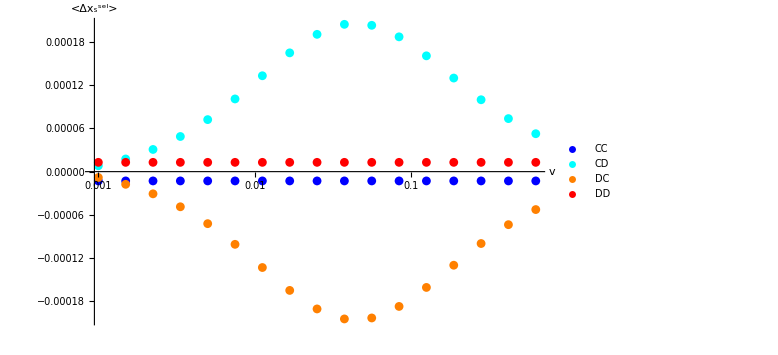

```mathematica
ListLogLinearPlot[{dataCC,dataCD,dataDC,dataDD},
AxesLabel->{"v","<Δx_s^sel>"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},Automatic},
ImageSize->Large,PlotRange->All,PlotStyle->{Blue,Cyan,Orange,Red}]
```

```mathematica
hcalc2[40,0,0.001,0]
```

0.980354